```mathematica
P := Function[{c},Function[{z},z^2+c]]
```

```mathematica
ConvergesIn := Function[{i,f,x},If[Abs[f[x]] ≥ 2 || i ==0 ,i, ConvergesIn[i-1,f,f[x]]]]
```

```mathematica
F := Function[{x,y,m},ConvergesIn[m,P[x+y I],0]]
```

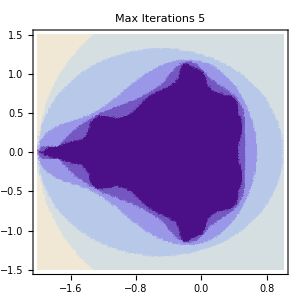
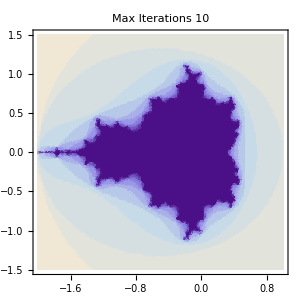
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
DensityPlot[F[x,y,maxIter],{x,-2,1},{y,-1.5,1.5},
PlotPoints-> 80,
ImageSize -> 300,
PlotLabel -> "Max Iterations " <> ToString[maxIter]
],
{maxIter,{5,10,20,50}}
]
```